```mathematica
alphaIII=delta-Pi;
alpha0=0;
alpha1=-(2*alpha0-2*alphaIII+1*delta)/delta;
alpha3=2*(alpha0-alphaIII+1*delta)/(delta*delta*delta);
alpha4=-(alpha0-alphaIII+1*delta)/(delta*delta*delta*delta);

alphaiota[varphi_,delta_]=Piecewise[
{
{alpha0+alpha1 varphi+alpha3 varphi^3+alpha4 varphi^4,0≤varphi≤delta},
{varphi-Pi,delta<varphi<2π-delta},
{-(alpha0+alpha1(2Pi-varphi)+alpha3((2Pi-varphi)^3)+alpha4((2Pi-varphi)^4)),2π-delta≤varphi≤2π}
}
];
```

```mathematica
alphashift=-π/2;
nforalpha=1;
alphaIII=0;
alpha0=-Pi*nforalpha;
alpha1=-(2*alpha0-2*alphaIII+0*delta)/delta;
alpha3=2*(alpha0-alphaIII+0*delta)/(delta*delta*delta);
alpha4=-(alpha0-alphaIII+0*delta)/(delta*delta*delta*delta);

alphanotiota[varphi_,delta_]=Piecewise[
{
{alphashift+alpha0+alpha1*varphi+alpha3*(varphi^3)+alpha4*(varphi^4),0≤varphi≤delta},
{alphashift,delta<varphi<2π-delta},
{alphashift-(alpha0+alpha1*(2*Pi-varphi)+alpha3*((2*Pi-varphi)^3)+alpha4*((2*Pi-varphi)^4)),2π-delta≤varphi≤2π}
}
];
```

```mathematica
alpha[varphi_,delta_,iota_]=FullSimplify[iota alphaiota[varphi,delta]+alphanotiota[varphi,delta]];
```

```mathematica
gamma[varphi_,delta_,iota_]=FullSimplify[iota-D[alpha[varphi,delta,iota],varphi]]
```

Piecewise[{{(2 (-1+iota) π (delta-varphi)^2 (delta+2 varphi))/delta^4, varphi≥0&&delta≥varphi}, {0, delta<varphi&&delta+varphi<2 π}, {(2 (-1+iota) π (delta+4 π-2 varphi) (delta-2 π+varphi)^2)/delta^4, delta+varphi≥2 π&&varphi≤2 π}, {iota, True}}]

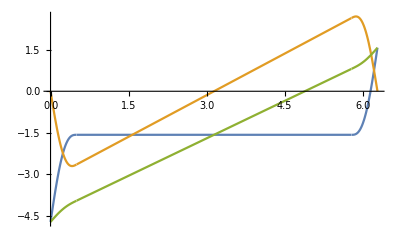

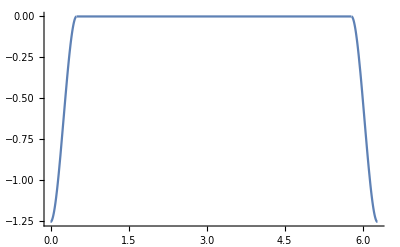

```mathematica
deltaa=0.5;iotaa=0.9;
Plot[{alphanotiota[x,deltaa],alphaiota[x,deltaa],alpha[x,deltaa,iotaa]},{x,0,2π}]
Plot[gamma[x,deltaa,iotaa],{x,0,2π},PlotRange->All]
```

```mathematica
alpha[φ,δ,iota]
```

Piecewise[{{(-4 (-1+iota) π δ^3 φ+4 (-1+iota) π δ φ^3-2 (-1+iota) π φ^4+δ^4 (-3 π+2 iota φ))/(2 δ^4), φ≥0&&δ≥φ}, {-1/2 (1+2 iota) π+iota φ, δ<φ&&δ+φ<2 π}, {(1/2-2 iota) π+(2 (-1+iota) π (2 π-φ))/δ-(2 (-1+iota) π (2 π-φ)^3)/δ^3+iota φ+((-1+iota) π (-2 π+φ)^4)/δ^4, δ+φ≥2 π&&φ≤2 π}, {0, True}}]

```mathematica
gamma[φ,δ,iota]
```

Piecewise[{{(2 (-1+iota) π (δ-φ)^2 (δ+2 φ))/δ^4, φ≥0&&δ≥φ}, {0, δ<φ&&δ+φ<2 π}, {(2 (-1+iota) π (4 π+δ-2 φ) (-2 π+δ+φ)^2)/δ^4, δ+φ≥2 π&&φ≤2 π}, {iota, True}}]